```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M0-g,v[0]==0},v[t],t]

v1[t_]=v[t]/.sol1[[1]]

M[t_]=M0-A1*ve*1000*t
sol2=DSolve[{v'[t]==-(ve/M[t])*M'[t]-g,v[0]==vi1},v[t],t]
v2[t_]=v[t]/.sol2[[1]]

sol3=DSolve[{v'[t]==-g-(k*c*(v[t])^(2))/(M2),v[0]==vi2},v[t],t]
v3[t_]=v[t]/.sol3[[1]]

sol4=DSolve[{v'[t]==-g+(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
v4[t_]=v[t]/.sol4[[1]]
```

{{v[t]→(-g M0 t+A1 P1 t)/M0}}

(-g M0 t+A1 P1 t)/M0

M0-1000 A1 t ve

{{v[t]→-g t+vi1+ve Log[M0]-ve Log[M0-1000 A1 t ve]}}

-g t+vi1+ve Log[M0]-ve Log[M0-1000 A1 t ve]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k vi2)/(√g √M2)])/(√M2)])/(√c √k)}}

(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k vi2)/(√g √M2)])/(√M2)])/(√c √k)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→-(√g √M2 Tanh[(√c √g √k t)/(√M2)])/(√c √k)}}

-(√g √M2 Tanh[(√c √g √k t)/(√M2)])/(√c √k)

```mathematica
h1[t_]=Integrate[v1[t],t]
```

-(g t^2)/2+(A1 P1 t^2)/(2 M0)

```mathematica
h2[t_]=Integrate[v2[t],t]
```

-(g t^2)/2+t ve+t vi1+t ve Log[M0]+(M0 Log[M0-1000 A1 t ve])/(1000 A1)-t ve Log[M0-1000 A1 t ve]

```mathematica
h3[t_]=Integrate[v3[t],t]
```

(M2 Log[Cos[(√c √g √k t)/(√M2)-ArcTan[(√c √k vi2)/(√g √M2)]]])/(c k)

```mathematica
h4[t_]=Integrate[v4[t],t]
```

-(M2 Log[Cosh[(√c √g √k t)/(√M2)]])/(c k)

```mathematica
a1[t_]=D[v1[t],t]
```

(-g M0+A1 P1)/M0

```mathematica
a2[t_]=D[v2[t],t]
```

-g+(1000 A1 ve^2)/(M0-1000 A1 t ve)

```mathematica
a3[t_]=D[v3[t],t]
```

-g Sec[(-√c √g √k t+√M2 ArcTan[(√c √k vi2)/(√g √M2)])/(√M2)]^2

```mathematica
a4[t_]=D[v4[t],t]
```

-g Sech[(√c √g √k t)/(√M2)]^2

```mathematica
tsol1=Solve[h1[t]==L,t]
vi1=Simplify[v1[t]/.tsol1[[2]]]
```

{{t→-(√2 √L)/(√(-g+(A1 P1)/M0))},{t→(√2 √L)/(√(-g+(A1 P1)/M0))}}

√2 √L √(-g+(A1 P1)/M0)

```mathematica
t1=tsol1[[2]]
```

{t→(√2 √L)/(√(-g+(A1 P1)/M0))}

```mathematica
t1=t/.t1
```

(√2 √L)/(√(-g+(A1 P1)/M0))

```mathematica
h02=h1[t1]
```

-(g L)/(-g+(A1 P1)/M0)+(A1 L P1)/(M0 (-g+(A1 P1)/M0))

```mathematica
h2[t]=h2[t]+h02
```

-(g L)/(-g+(A1 P1)/M0)+(A1 L P1)/(M0 (-g+(A1 P1)/M0))+√2 √L √(-g+(A1 P1)/M0) t-(g t^2)/2+t ve+t ve Log[M0]+(M0 Log[M0-1000 A1 t ve])/(1000 A1)-t ve Log[M0-1000 A1 t ve]

```mathematica
M[t_]=M0-A1*ve*1000*t
t2=M1/(A1*ve*1000)
vi2=v2[t2]
h03=h2[t2]
h3[t]=h3[t]+h03
```

M0-1000 A1 t ve

M1/(1000 A1 ve)

√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]

M1/(1000 A1)-(g M1^2)/(2000000 A1^2 ve^2)+(√L M1 √(-g+(A1 P1)/M0))/(500 √2 A1 ve)+(M1 Log[M0])/(1000 A1)+(M0 Log[M0-M1])/(1000 A1)-(M1 Log[M0-M1])/(1000 A1)

M1/(1000 A1)-(g M1^2)/(2000000 A1^2 ve^2)+(√L M1 √(-g+(A1 P1)/M0))/(500 √2 A1 ve)+(M1 Log[M0])/(1000 A1)+(M0 Log[M0-M1])/(1000 A1)-(M1 Log[M0-M1])/(1000 A1)+(M2 Log[Cos[(√c √g √k t)/(√M2)-ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)]]])/(c k)

```mathematica
tsol3=Solve[v3[t]==0,t]
t3=tsol3[[1]]
t3=t/.t3 
t3=t3+t2
h04=h3[t3]
h4[t]=h4[t]+h04
```

{{t→(√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)])/(√c √g √k)}}

{t→(√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)])/(√c √g √k)}

(√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)])/(√c √g √k)

M1/(1000 A1 ve)+(√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)])/(√c √g √k)

1/(c k)M2 Log[Cos[ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)]-(√c √g √k (M1/(1000 A1 ve)+(√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)])/(√c √g √k)))/(√M2)]]

1/(c k)M2 Log[Cos[ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)]-(√c √g √k (M1/(1000 A1 ve)+(√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)])/(√c √g √k)))/(√M2)]]-(M2 Log[Cosh[(√c √g √k t)/(√M2)]])/(c k)

```mathematica
tsol4=Solve[h4[t]==0,t]
t4=tsol4[[1]]
t4=t/.t4 
t4=t4+t3
```

{{t→ConditionalExpression[1/(√c √g √k)√M2 (-ArcCosh[Cos[ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)]-(√c √g √k (M1/(1000 A1 ve)+(√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)])/(√c √g √k)))/(√M2)]]+2 ⅈ π C[1]),C[1]∈ℤ&&-π<Im[Log[Cos[ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)]-(√c √g √k (M1/(1000 A1 ve)+(√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)])/(√c √g √k)))/(√M2)]]]≤π]},{t→ConditionalExpression[1/(√c √g √k)√M2 (ArcCosh[Cos[ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)]-(√c √g √k (M1/(1000 A1 ve)+(√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)])/(√c √g √k)))/(√M2)]]+2 ⅈ π C[1]),C[1]∈ℤ&&-π<Im[Log[Cos[ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)]-(√c √g √k (M1/(1000 A1 ve)+(√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)])/(√c √g √k)))/(√M2)]]]≤π]}}

{t→ConditionalExpression[1/(√c √g √k)√M2 (-ArcCosh[Cos[ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)]-(√c √g √k (M1/(1000 A1 ve)+(√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)])/(√c √g √k)))/(√M2)]]+2 ⅈ π C[1]),C[1]∈ℤ&&-π<Im[Log[Cos[ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)]-(√c √g √k (M1/(1000 A1 ve)+(√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)])/(√c √g √k)))/(√M2)]]]≤π]}

ConditionalExpression[1/(√c √g √k)√M2 (-ArcCosh[Cos[ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)]-(√c √g √k (M1/(1000 A1 ve)+(√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)])/(√c √g √k)))/(√M2)]]+2 ⅈ π C[1]),C[1]∈ℤ&&-π<Im[Log[Cos[ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)]-(√c √g √k (M1/(1000 A1 ve)+(√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)])/(√c √g √k)))/(√M2)]]]≤π]

ConditionalExpression[M1/(1000 A1 ve)+(√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)])/(√c √g √k)+1/(√c √g √k)√M2 (-ArcCosh[Cos[ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)]-(√c √g √k (M1/(1000 A1 ve)+(√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)])/(√c √g √k)))/(√M2)]]+2 ⅈ π C[1]),C[1]∈ℤ&&-π<Im[Log[Cos[ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)]-(√c √g √k (M1/(1000 A1 ve)+(√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)])/(√c √g √k)))/(√M2)]]]≤π]

```mathematica
L=.22
A1=((4.75*10^(-3))^2)*Pi
A2=((.06)^2)*Pi
P1=4.4*10^5
P2=10^5
M0=0.6889
M1=.5
M2=.1889
g=9.81
ve=26.07680962
ρ1=1000
ρ2=1.22
c=0.1
k=ρ2*A2/2
```

0.22

0.0000708822

0.0113097

440000.

100000

0.6889

0.5

0.1889

9.81

26.0768

1000

1.22

0.1

0.00689894

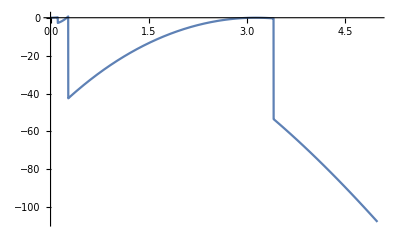

```mathematica
hcom[t_]:=h1[t]/;t<t1 
hcom[t_]:=h2[t]/;t1<t<t2 
hcom[t_]:=h3[t]/;t2<t<t3
hcom[t_]:=h4[t]/;t3<t<5
Plot[hcom[t],{t,0,5}]
```

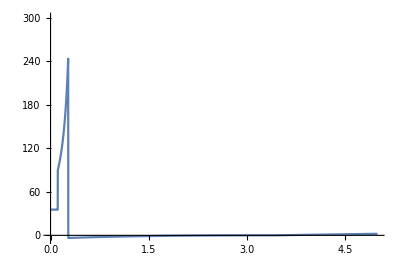

```mathematica
acom[t_]:=a1[t]/;t<t1
acom[t_]:=a2[t]/;t1<t<t2
acom[t_]:=a3[t]+9.8/;t2<t<t3
acom[t_]:=a4[t]+6.6/;t3<t<5

Plot[acom[t],{t,0,5},PlotRange->{-5,300}, AspectRatio->2/3]
```

```mathematica
5
```

5

```mathematica
a1
```

a1

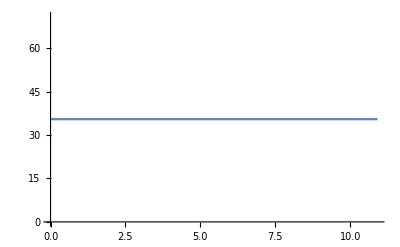

```mathematica
Plot[a1[t],{t,0,10.91}]
```

```mathematica
a1[t]
```

35.4624

```mathematica
A1*P1
```

31.1882

```mathematica
A1
```

0.0000708822